```mathematica
η=10^-9;
Γ=1/880;
g[t_]:=7.25+10 E^(-((t-10)/5)^2);
(*MeV=10^22/6.58 1/sec*)
Subscript[M, pl]=1.22/6.58 10^44;
m=1000/6.58 10^22;
Subscript[m, π]=140 10^22/6.58; α=1/137;
T[t_]:=TT/.First[Solve[TT==√(Subscript[M, pl]/(2t))((8π)/3 π^3/30 g[t])^(-1/4),TT]];
H[t_]:=1/(2t);
Subscript[n, γ][t_]:=2/π^2 Zeta[3] T[t]^3;
Δ=2.22/6.58 10^22;
```

## Physical frame

```mathematica
t0=5;
t1=20000;
```

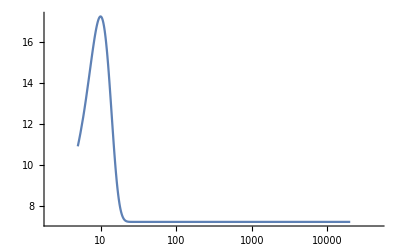

```mathematica
LogLinearPlot[g[t],{t,t0,t1},PlotRange->All]
```

```mathematica
sols=NDSolve[{
D[Subscript[n, n][t], t]+3H[t]Subscript[n, n][t]== -Γ Subscript[n, n][t]-(D[Subscript[n, D][t], t]+3H[t]Subscript[n, D][t]),
D[Subscript[n, p][t], t]+3H[t]Subscript[n, p][t]== +Γ Subscript[n, n][t]-(D[Subscript[n, D][t], t]+3H[t]Subscript[n, D][t]),
D[Subscript[n, D][t], t]+3H[t]Subscript[n, D][t]==α/Subscript[m, π]^2(√((3 T[t])/m)Subscript[n, n][t]Subscript[n, p][t]-E^(-Δ/T[t])Subscript[n, D][t]Subscript[n, γ][t]),
Subscript[n, n][t0]== 1/7 η Subscript[n, γ][t0],
Subscript[n, p][t0]== 6/7 η Subscript[n, γ][t0],
Subscript[n, D][t0]==(√((3 T[t0])/m)Subscript[n, n][t0]Subscript[n, p][t0])/(E^(-Δ/T[t0])Subscript[n, γ][t0])
}//FullSimplify,{Subscript[n, n][t],Subscript[n, p][t],Subscript[n, D][t]},{t,t0,t1}]//First//Values;
```

```mathematica
sols
```

{InterpolatingFunction[{{5., 20000.}}, <>][t],InterpolatingFunction[{{5., 20000.}}, <>][t],InterpolatingFunction[{{5., 20000.}}, <>][t]}

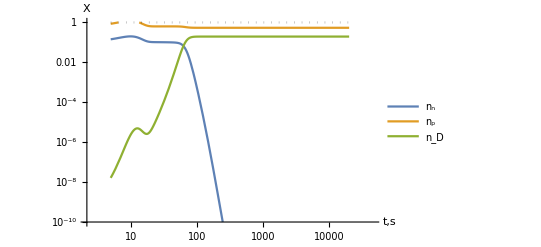

0.195668

```mathematica
LogLogPlot[{
sols[[1]]/(η Subscript[n, γ][t]),
sols[[2]]/(η Subscript[n, γ][t]),
2sols[[3]]/(η Subscript[n, γ][t]),
1
},{t,t0,t1},PlotRange->{10^-10,1},PlotLegends->{"n_n","n_p","n_D"},PlotStyle->{,,,{Opacity[0.3],Black,Dotted}},AxesLabel->{"t,s","X"}]
2sols[[3]]/(η Subscript[n, γ][t])/.t->t1
```

```mathematica
0.25696583290132624
```

```mathematica
0.26675013502727446
```

## Comoving frame

```mathematica
a[t_]:=√(t/t0);
sols=NDSolve[{
D[Subscript[n, n][t], t]== -Γ Subscript[n, n][t]-D[Subscript[n, D][t], t],
D[Subscript[n, p][t], t]== +Γ Subscript[n, n][t]-D[Subscript[n, D][t], t],
D[Subscript[n, D][t], t]==α/(Subscript[m, π]^2 a[t]^3)(√((3 T[t])/m)Subscript[n, n][t]Subscript[n, p][t]-E^(-Δ/T[t])Subscript[n, D][t]Subscript[n, γ][t]),
Subscript[n, n][t0]== 1/7 η Subscript[n, γ][t0] a[t0]^3,
Subscript[n, p][t0]== 6/7 η Subscript[n, γ][t0] a[t0]^3,
Subscript[n, D][t0]==(√((3 T[t0])/m)Subscript[n, n][t0]Subscript[n, p][t0])/(E^(-Δ/T[t0])Subscript[n, γ][t0])a[t0]^3
}//FullSimplify,{Subscript[n, n][t],Subscript[n, p][t],Subscript[n, D][t]},{t,t0,t1}]//First//Values;
```

```mathematica
sols
```

{InterpolatingFunction[{{5., 200.}}, <>][t],InterpolatingFunction[{{5., 200.}}, <>][t],InterpolatingFunction[{{5., 200.}}, <>][t]}

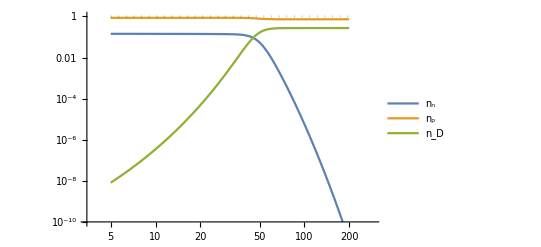

```mathematica
LogLogPlot[{
sols[[1]]/(η Subscript[n, γ][t] a[t]^3),
sols[[2]]/(η Subscript[n, γ][t] a[t]^3),
2sols[[3]]/(η Subscript[n, γ][t] a[t]^3),
1
},{t,t0,t1},PlotRange->{10^-10,1},PlotLegends->{"n_n","n_p","n_D"},PlotStyle->{,,,{Opacity[0.3],Black,Dotted}}]
```